/homes/ht/Desktop/today2/dev/N5/results/Intact

{{L:,40.},{m:,40},{N:,5},{kappa:,0.1},{sigma:,0.0012},{kappa_sigma_r:,83.3333},{Delta:,0.4938},{Extension Minimum:,0},{Extension Maximum:,10},{e0:,0.04},{Beta:,38.6817}}

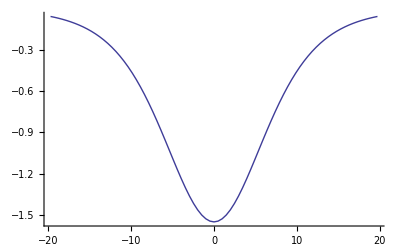

Backbone spring constant κ:

0.1

Base-pair spring constant σ(ϵ = 0.04):

0.0012

κ/σ ratio:

83.3333

```mathematica
Needs["PlotLegends`"]
<<Units`
<<PhysicalConstants`

SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
Parameters=Import["../Parameters"]
Potential=Import["../Potential_Data.out","Table"];
ListLinePlot[Potential,PlotStyle->{Thick},AxesOrigin->{0,0},PlotRange->All]

IntactPF=Import["PartitionFunction_0_0.out","Table"];
IntactFE=Import["FreeEnergy_0_0.out","Table"];
IntactdFE=Import["dFreeEnergy_0_0.out","Table"];

IntactZNJη=Import["znj_eta.out","Table"];
IntactZNJξ=Import["znj_xi.out","Table"];

IntactMXDη=Import["MeanAxialDisp_eta.out","Table"];
IntactMXDξ=Import["MeanAxialDisp_xi.out","Table"];

AverageX= Import["Average_X.out","Table"];
AverageY= Import["Average_Y.out","Table"];

fsTitle=24;
fsAxesLabel=18;
fs2=16;

T=300 SI[Kelvin];
n=Parameters[[3,2]];
Print["Backbone spring constant κ:"]
κ=Parameters[[4,2]]
Print["Base-pair spring constant σ(ϵ = "<>ToString[ϵ]<>"):"]
σ=Parameters[[5,2]]
Print["κ/σ ratio:"]
κσr=Parameters[[6,2]]
Δ=Parameters[[7,2]];

umin=Parameters[[8,2]];
umax=Parameters[[9,2]];

ϵ=Parameters[[10,2]];(*eV*)
β=Parameters[[11,2]];(*eV^-1*) 

Subscript[η, B]=2.0;

ToNewton=Convert[ElectronVolt/Angstrom,Newton] SI[Pico Newton]^-1 ;(*Converts eV/Å to pN*)
ToForceDimension[f_]:=(f(κ/(4β))^(1/2)) ToNewton;
ToDimension[η_]:=η((κ β)/4)^(-1/2)(*Converts to Å*)
```

### Length Dimension Check

```mathematica
Subscript[η, B] (*No Dimension*)
ToDimension[Subscript[η, B]] (*Å*)
```

2.

2.0338

### Force Dimension Check

```mathematica
0.5 (*No Dimension*)
σ ToDimension[Subscript[η, B]] ToNewton  (*pN*)
ToForceDimension[0.5] (*Converts force to dimensions of eV/Å then to J/m for pN*)
```

0.5

3.9102

20.3656

## Numerical Results

### Partition Function & Free Energy

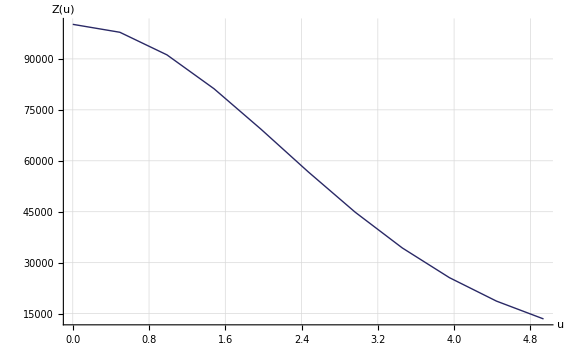
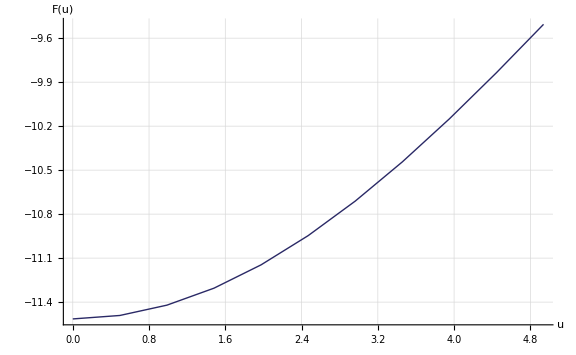

```mathematica
pIntactPF=ListLinePlot[
IntactPF,
ImageSize->Large,
PlotStyle->{Thick,Darker[ColorData[1,1]]},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
PlotRange->All,
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["Z(u)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}
];

pIntactFE=ListLinePlot[
IntactFE,
ImageSize->Large,
PlotStyle->{Thick,Darker[ColorData[1,1]]},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
PlotRange->All,
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["F(u)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}
];

{pIntactPF,pIntactFE}
```

### Mean Axial Displacement of ξ and η

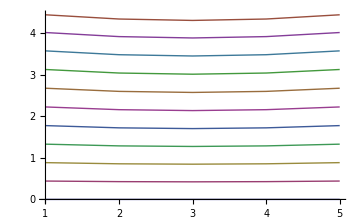
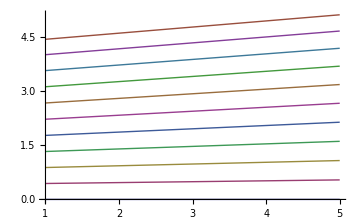

2.22095

0 | 0 | 0 | 0 | 0
0.441538 | 0.427412 | 0.422735 | 0.427412 | 0.441538
0.883694 | 0.855694 | 0.846423 | 0.855694 | 0.883694
1.32728 | 1.28592 | 1.27222 | 1.28592 | 1.32728
1.773 | 1.71904 | 1.70116 | 1.71904 | 1.773
2.22095 | 2.1554 | 2.13367 | 2.1554 | 2.22095
2.67049 | 2.59459 | 2.56941 | 2.59459 | 2.67049
3.12018 | 3.03535 | 3.00719 | 3.03535 | 3.12018
3.56743 | 3.47527 | 3.44465 | 3.47527 | 3.56743
4.00779 | 3.91004 | 3.87754 | 3.91004 | 4.00779
4.43382 | 4.33232 | 4.29853 | 4.33232 | 4.43382

Extension U (End base-pair separations at η_B) = 5

Extension U in terms of η = 2.469 (5Δ)

```mathematica
{ListLinePlot[IntactMXDη,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}],
ListLinePlot[IntactMXDξ,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}]}
NearestValue=Nearest[Transpose[Chop[IntactMXDη,10^-5]][[1]],Subscript[η, B]][[1]]
upos=Flatten[Position[Transpose[Chop[IntactMXDη,10^-5]][[1]],NearestValue]][[1]];
U=upos-1;
Grid[Chop[IntactMXDη,10^-5],Background->{Automatic,{upos->Yellow}}]
Print["Extension U (End base-pair separations at η_B) = ",U]
Print["Extension U in terms of η = ",U Δ," (",U,"Δ)"]
```

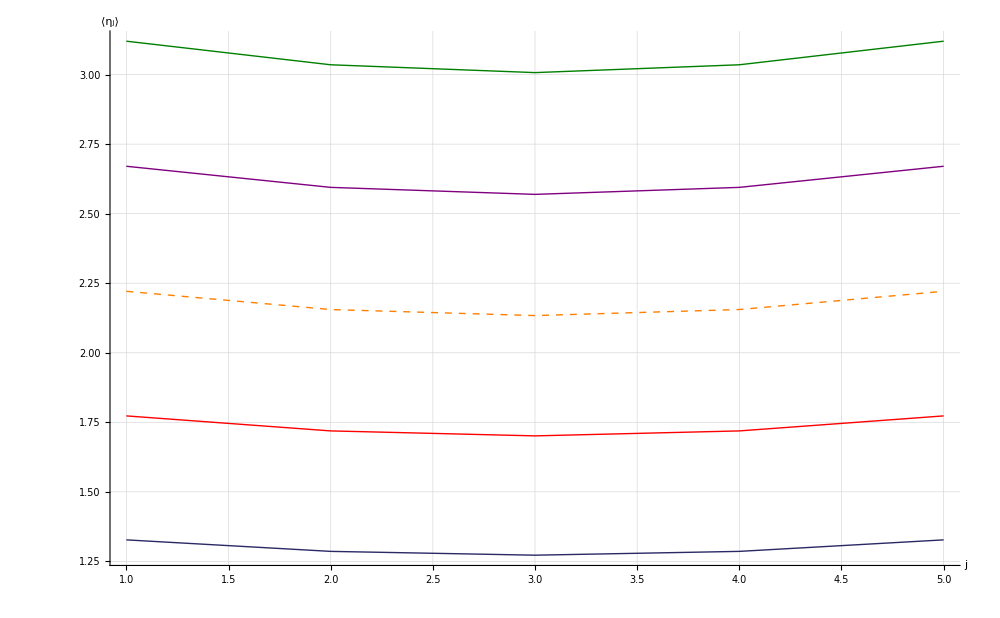

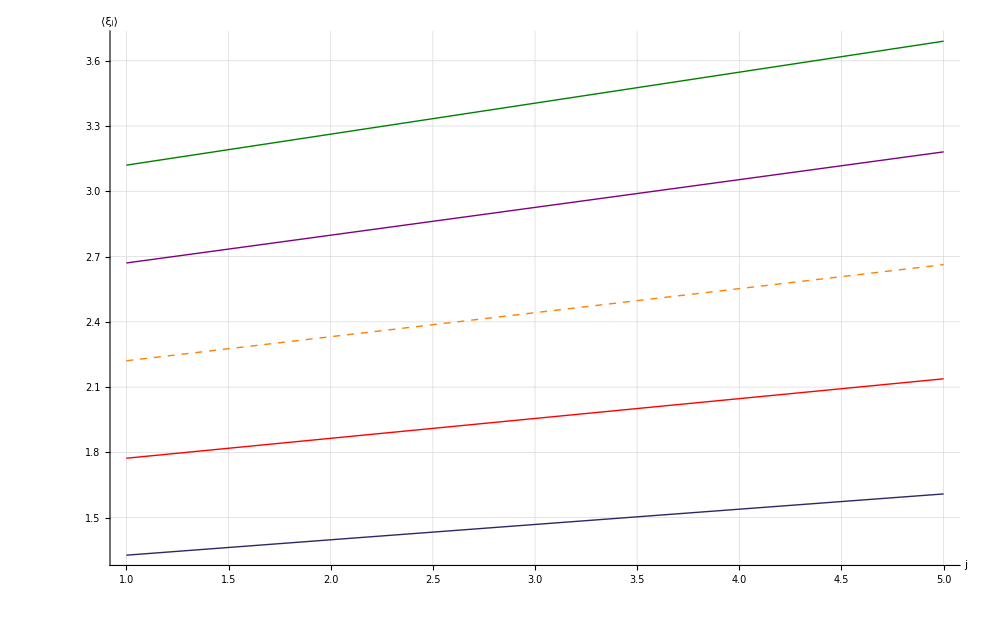

18.6796

```mathematica
pos1=upos-2;
pos2=upos-1;
pos3=upos;
pos4=upos+1;
pos5=upos+2;

pIntactMXDη=ListLinePlot[
{
IntactMXDη[[pos1]],
IntactMXDη[[pos2]],
IntactMXDη[[pos3]],
IntactMXDη[[pos4]],
IntactMXDη[[pos5]]
},
ImageSize->1000,
PlotStyle->{
{Thick,Darker[ColorData[1,1]]},
{Thick,Red},
{Thick,Dashed,Orange},
{Thick,Purple},
{Thick,Darker[Green,0.5]}
},
PlotLegend->{
Style["u="<>ToString[(pos1-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos2-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos3-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos4-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos5-1)Δ],FontSize->fs2]
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
PlotRange->All,
AxesOrigin->{1,0},
AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["⟨η_j⟩",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->0.55,
LegendPosition->{0.9,-.2}
]

pIntactMXDξ=ListLinePlot[
{
IntactMXDξ[[pos1]],
IntactMXDξ[[pos2]],
IntactMXDξ[[pos3]],
IntactMXDξ[[pos4]],
IntactMXDξ[[pos5]]
},
ImageSize->1000,
PlotStyle->{
{Thick,Darker[ColorData[1,1]]},
{Thick,Red},
{Thick,Dashed,Orange},
{Thick,Purple},
{Thick,Darker[Green,0.5]}
},
PlotLegend->{
Style["u="<>ToString[(pos1-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos2-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos3-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos4-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos5-1)Δ],FontSize->fs2]
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
PlotRange->All,
AxesOrigin->{1,0},
AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["⟨ξ_j⟩",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->0.55,
LegendPosition->{0.9,-.2}
]
```

### Force-Extension

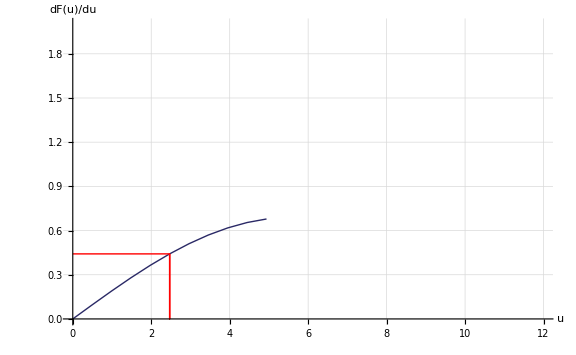

Dimensionless force at (U = 5Δ) = 0.441603

Dimensional Force = 17.987 pN
Dimensional Extension = 2.51086 Å

Dimensional Resultant Average Force = 18.6796 pN

```mathematica
fpos={{0,IntactdFE[[upos]][[2]]},{IntactdFE[[upos]][[1]],IntactdFE[[upos]][[2]]},{IntactdFE[[upos]][[1]],0},{IntactdFE[[upos]][[1]],IntactdFE[[upos]][[2]]}};
F=IntactdFE[[upos]][[2]];
u = IntactdFE[[upos]][[1]];

Subscript[resF, c]=(κ (ToDimension[AverageX[[upos]][[n]]-AverageX[[upos]][[n-1]]])+σ (ToDimension[AverageX[[upos]][[n]] -AverageY[[upos]][[n]]]))ToNewton;

pIntactPF=ListLinePlot[
{
IntactdFE,
fpos
},
ImageSize->Large,
PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red}},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
PlotRange->{{0,12},{0,2}},
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["dF(u)/du",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}
]
Print["Dimensionless force at (U = ",U,"Δ) = ",F]

Subscript[F, c]=ToForceDimension[F];
Print["\nDimensional Force = ",Subscript[F, c] pN,"\nDimensional Extension = ",ToDimension[u]Å,"\n\nDimensional Resultant Average Force = ",Subscript[resF, c] pN,"\n"]
Export["N"<>ToString[n]<>"_sim.data",{{n,Subscript[F, c],Subscript[resF, c],NearestValue,κσr}},"Table"];
```

### Average X and Y

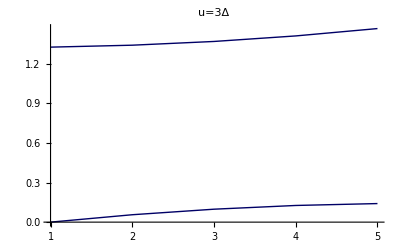
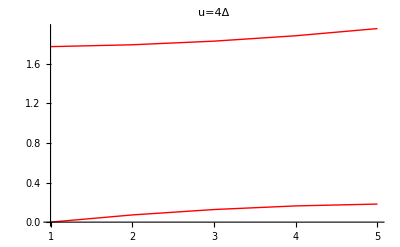
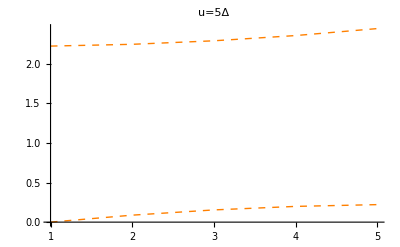
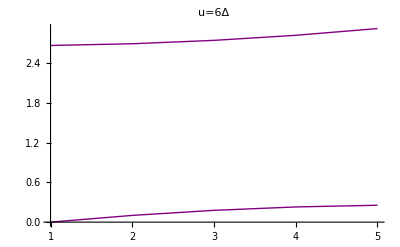
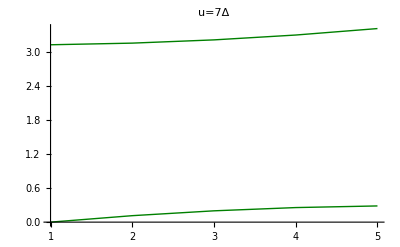

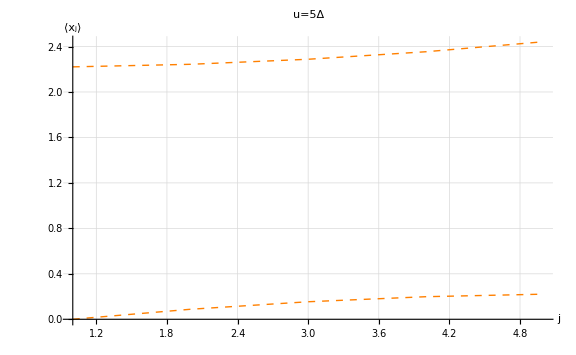

```mathematica
avg1=ListLinePlot[{Chop[AverageX[[pos1]]],Chop[AverageY[[pos1]]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Darker[Blue,0.6]}},PlotLabel->"u="<>ToString[pos1-1]<>"Δ"];
avg2=ListLinePlot[{AverageX[[pos2]],AverageY[[pos2]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Red}},PlotLabel->"u="<>ToString[pos2-1]<>"Δ"];
avg3=ListLinePlot[{AverageX[[pos3]],AverageY[[pos3]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Dashed,Orange}},PlotLabel->"u="<>ToString[pos3-1]<>"Δ"];
avg4=ListLinePlot[{AverageX[[pos4]],AverageY[[pos4]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Purple}},PlotLabel->"u="<>ToString[pos4-1]<>"Δ"];
avg5=ListLinePlot[{AverageX[[pos5]],AverageY[[pos5]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Darker[Green,0.5]}},PlotLabel->"u="<>ToString[pos5-1]<>"Δ"];
{avg1,avg2,avg3,avg4,avg5}
Show[avg3,ImageSize->Large,GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["⟨x_j⟩",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}]
```